# HW 2

{0.155633,Null}

{0.0898175,Null}

{True,True}

{5.10703×10^-16,8.21536×10^-16}

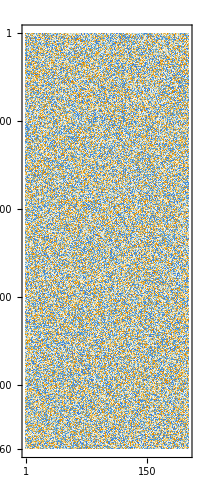
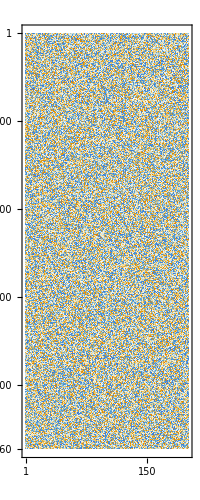

```mathematica
{m,n}= {9460,200};
A=RandomReal[{-1,1},{m,n}];
AbsoluteTiming[Q1= Orthogonalize[Aᵀ]ᵀ;]
AbsoluteTiming[Q2= QRDecomposition[A]⟦1⟧ᵀ;]
Map[OrthogonalMatrixQ,{Q1,Q2}]
Map[ Norm[#ᵀ.#-IdentityMatrix[n]]&,{Q1,Q2}]
Map[MatrixPlot,{Q1,Q2}]
```